```mathematica
Remove["Global`*"];
```

```mathematica
PDF1= (-t^2*((t-8)*t^2+π*(6*t-4)));
```

```mathematica
PDF2 =2 *t*(t^2*(t^2-8* Sqrt[t^2 - 1]+3)-4*Sqrt[t^2-1]+12*t^2*ArcCos[(1/t)]+π*(3-4*t)-(1/2));
```

```mathematica
PDF3=t*((1+t^2)*(6 * π+8 *Sqrt[t^2-2]-5 -t^2)-16*t*ArcSin[1/Sqrt[2-2/t^(2)]]+16*t*ArcTan[t*Sqrt[t^2-2]]-24*(1+t^2)*ArcTan[(Sqrt[t^2-2])]);
```

```mathematica
a={t∈Reals,L∈Reals,t >=0, L> 0 ,t≤1};
CDF1 = FullSimplify[Integrate[PDF1, t,Assumptions->a],a];
```

```mathematica
b={t∈Reals,L∈Reals,t > 1 , L> 0 ,t≤Sqrt[2]};
CDF2A= FullSimplify[Integrate[PDF2, t, Assumptions->b]  ,b];
```

```mathematica
CDF2 =  FullSimplify[CDF2A  - (Function[t, Evaluate[CDF2A]][1] - Function[t, Evaluate[CDF1]][1])];
```

```mathematica
c={t∈Reals,L∈Reals,t > Sqrt[2] , L> 0 ,t≤ Sqrt[3]};
CDF3A=FullSimplify[Integrate[PDF3, t, Assumptions->c],c];
CDF3 =  FullSimplify[CDF3A  + (1  - Function[t, Evaluate[CDF3A]][Sqrt[3]])];
```

```mathematica
CForm[Evaluate[CDF1]]
```

(Power(t,3)*(5*Pi*(8 - 9*t) + (48 - 5*t)*Power(t,2)))/30.

```mathematica
CForm[Evaluate[CDF2]]
```

(3 + 10*Power(t,6) + 24*Sqrt(-1 + Power(t,2)) - 5*Pi*(3 + 2*Power(t,2)*(-9 + 8*t)) + Power(t,4)*(45 - 96*Sqrt(-1 + Power(t,2))) - 
     3*Power(t,2)*(5 + 36*Sqrt(-1 + Power(t,2))) + 180*Power(t,4)*ArcSec(t))/30.

```mathematica
CForm[Evaluate[CDF3]]
```

(3*(9 + 5*Pi) + 15*(-5 + 6*Pi)*Power(t,2) + 45*(-1 + Pi)*Power(t,4) - 5*Power(t,6) + 12*Sqrt(-2 + Power(t,2)) + 108*Power(t,2)*Sqrt(-2 + Power(t,2)) + 
     48*Power(t,4)*Sqrt(-2 + Power(t,2)) + 30*ArcTan((-2 + t)/Sqrt(-2 + Power(t,2))) - 30*ArcTan((2 + t)/Sqrt(-2 + Power(t,2))) - 
     20*Power(t,2)*(8*t*ArcCsc(Sqrt(2 - 2/Power(t,2))) + 9*(2 + Power(t,2))*ArcTan(Sqrt(-2 + Power(t,2))) - 8*t*ArcTan(t*Sqrt(-2 + Power(t,2)))))/30.

```mathematica
TeXForm[Evaluate[CDF1]]
```

\frac{1}{30} t^3 \left((48-5 t) t^2+5 \pi  (8-9 t)\right)

```mathematica
TeXForm[Evaluate[CDF2]]
```

\frac{1}{30} \left(10 t^6+180 t^4 \sec ^{-1}(t)-3 \left(36 \sqrt{t^2-1}+5\right) t^2-5 \pi  \left(2 (8 t-9) t^2+3\right)+24 \sqrt{t^2-1}+\left(45-96
   \sqrt{t^2-1}\right) t^4+3\right)

```mathematica
TeXForm[Evaluate[CDF3]]
```

\frac{1}{30} \left(-5 t^6+45 (\pi -1) t^4+108 \sqrt{t^2-2} t^2+15 (6 \pi -5) t^2+12 \sqrt{t^2-2}+30 \tan ^{-1}\left(\frac{t-2}{\sqrt{t^2-2}}\right)-30 \tan
   ^{-1}\left(\frac{t+2}{\sqrt{t^2-2}}\right)-20 t^2 \left(9 \left(t^2+2\right) \tan ^{-1}\left(\sqrt{t^2-2}\right)-8 t \tan ^{-1}\left(t
   \sqrt{t^2-2}\right)+8 t \csc ^{-1}\left(\sqrt{2-\frac{2}{t^2}}\right)\right)+48 \sqrt{t^2-2} t^4+3 (9+5 \pi )\right)

```mathematica
TeXForm[Evaluate[PDF1]]
```

-t^2 \left((t-8) t^2+\pi  (6 t-4)\right)

```mathematica
TeXForm[Evaluate[PDF2]]
```

2 t \left(\left(t^2-8 \sqrt{t^2-1}+3\right) t^2-4 \sqrt{t^2-1}+12 t^2 \cos ^{-1}\left(\frac{1}{t}\right)+\pi  (3-4 t)-\frac{1}{2}\right)

```mathematica
TeXForm[Evaluate[PDF3]]
```

t \left(\left(t^2+1\right) \left(-t^2+8 \sqrt{t^2-2}+6 \pi -5\right)-16 t \sin ^{-1}\left(\frac{1}{\sqrt{2-\frac{2}{t^2}}}\right)-24 \left(t^2+1\right) \tan
   ^{-1}\left(\sqrt{t^2-2}\right)+16 t \tan ^{-1}\left(t \sqrt{t^2-2}\right)\right)

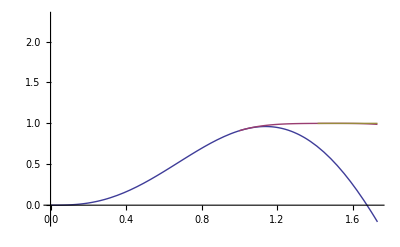

```mathematica
Plot[{CDF1, CDF2, CDF3},{t,0,Sqrt[3]}]
```